```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->-t]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
Clear[LEFT,SR]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Module[{J=Inverse[β[ω,δ,t,ϵ,m]],B:=Inverse[β[ω,δ,t,ϵ,m]],T1:=T1[t,m]},Do[J=Inverse[IdentityMatrix[2m]-B.ConjugateTranspose[T1].J.T1].B,10000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
SR[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ,m].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=SL[ω,δ,t,ϵ,m]=SR[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SL[ω,δ,t,ϵ,m].ρ[t,m].SR[ω,δ,t,ϵ,m].ρ[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,ϵ,m].ρ[t,m].SL[ω,δ,t,ϵ,m].ρ[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].ρ[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ,m].ρ[t,m].grr[ω,δ,t,ϵ,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ,m].ρ[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
left15= Compile[{ω},LEFT[ω,0.0001,1,0,15],CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
ParallelTable[{ω,-Im[left15[ω][[1,1]]]},{ω,Range[-2.5,2.5,0.01]}]
```

{{-2.5,0.131464},{-2.49,0.133395},{-2.48,0.134821},{-2.47,0.136324},{-2.46,0.137814},{-2.45,0.139497},{-2.44,0.140725},{-2.43,0.141923},{-2.42,0.142994},{-2.41,0.169394},{-2.4,0.191435},{-2.39,0.205423},{-2.38,0.217474},{-2.37,0.226828},{-2.36,0.234753},{-2.35,0.24261},{-2.34,0.24824},{-2.33,0.254344},{-2.32,0.259513},{-2.31,0.26515},{-2.3,0.270149},{-2.29,0.273943},{-2.28,0.278105},{-2.27,0.281381},{-2.26,0.283192},{-2.25,0.285917},{-2.24,0.289521},{-2.23,0.292229},{-2.22,0.2935},{-2.21,0.296293},{-2.2,0.298295},{-2.19,0.300875},{-2.18,0.3027},{-2.17,0.304081},{-2.16,0.305424},{-2.15,0.304614},{-2.14,0.304871},{-2.13,0.307194},{-2.12,0.308053},{-2.11,0.330462},{-2.1,0.372977},{-2.09,0.40083},{-2.08,0.418055},{-2.07,0.43304},{-2.06,0.444096},{-2.05,0.457077},{-2.04,0.468446},{-2.03,0.474673},{-2.02,0.482439},{-2.01,0.490261},{-2.,0.494268},{-1.99,0.500301},{-1.98,0.505323},{-1.97,0.511182},{-1.96,0.51359},{-1.95,0.517702},{-1.94,0.521436},{-1.93,0.525962},{-1.92,0.522325},{-1.91,0.530192},{-1.9,0.531807},{-1.89,0.528993},{-1.88,0.535555},{-1.87,0.534035},{-1.86,0.53435},{-1.85,0.5345},{-1.84,0.534687},{-1.83,0.535023},{-1.82,0.533886},{-1.81,0.531247},{-1.8,0.531304},{-1.79,0.531526},{-1.78,0.530947},{-1.77,0.530369},{-1.76,0.600814},{-1.75,0.653372},{-1.74,0.686643},{-1.73,0.713734},{-1.72,0.734926},{-1.71,0.749849},{-1.7,0.769062},{-1.69,0.771599},{-1.68,0.785472},{-1.67,0.7985},{-1.66,0.80449},{-1.65,0.818272},{-1.64,0.812076},{-1.63,0.82129},{-1.62,0.82635},{-1.61,0.829994},{-1.6,0.833103},{-1.59,0.832691},{-1.58,0.837361},{-1.57,0.838678},{-1.56,0.836852},{-1.55,0.832608},{-1.54,0.834127},{-1.53,0.833206},{-1.52,0.831026},{-1.51,0.837929},{-1.5,0.831206},{-1.49,0.833855},{-1.48,0.822475},{-1.47,0.819227},{-1.46,0.815031},{-1.45,0.817771},{-1.44,0.815589},{-1.43,0.800521},{-1.42,0.799557},{-1.41,0.800433},{-1.4,0.79083},{-1.39,0.811347},{-1.38,1.00919},{-1.37,1.08907},{-1.36,1.14546},{-1.35,1.18836},{-1.34,1.22237},{-1.33,1.24583},{-1.32,1.27258},{-1.31,1.29177},{-1.3,1.30642},{-1.29,1.31424},{-1.28,1.3309},{-1.27,1.33919},{-1.26,1.34056},{-1.25,1.34555},{-1.24,1.34659},{-1.23,1.34586},{-1.22,1.34207},{-1.21,1.34498},{-1.2,1.34014},{-1.19,1.33642},{-1.18,1.32761},{-1.17,1.3248},{-1.16,1.31209},{-1.15,1.30423},{-1.14,1.29382},{-1.13,1.28777},{-1.12,1.27202},{-1.11,1.25831},{-1.1,1.2415},{-1.09,1.23083},{-1.08,1.22428},{-1.07,1.20336},{-1.06,1.18881},{-1.05,1.16959},{-1.04,1.15704},{-1.03,1.15057},{-1.02,1.13299},{-1.01,1.16583},{-1.,626.088},{-0.99,1.12675},{-0.98,1.06843},{-0.97,1.04239},{-0.96,1.02093},{-0.95,0.998238},{-0.94,0.977741},{-0.93,0.957739},{-0.92,0.938733},{-0.91,0.919347},{-0.9,0.902274},{-0.89,0.879967},{-0.88,0.859105},{-0.87,0.833729},{-0.86,0.808381},{-0.85,0.79496},{-0.84,0.766471},{-0.83,0.749941},{-0.82,0.730803},{-0.81,0.709977},{-0.8,0.686482},{-0.79,0.661871},{-0.78,0.643995},{-0.77,0.622584},{-0.76,0.604197},{-0.75,0.576836},{-0.74,0.555808},{-0.73,0.532903},{-0.72,0.511535},{-0.71,0.486394},{-0.7,0.464932},{-0.69,0.443827},{-0.68,0.419291},{-0.67,0.394242},{-0.66,0.367985},{-0.65,0.341756},{-0.64,0.312467},{-0.63,0.284978},{-0.62,0.25246},{-0.61,0.186756},{-0.6,0.170215},{-0.59,0.166099},{-0.58,0.15866},{-0.57,0.153794},{-0.56,0.144976},{-0.55,0.138483},{-0.54,0.133868},{-0.53,0.130799},{-0.52,0.124599},{-0.51,0.117989},{-0.5,0.114869},{-0.49,0.108894},{-0.48,0.102573},{-0.47,0.0991607},{-0.46,0.0934459},{-0.45,0.0872262},{-0.44,0.0824713},{-0.43,0.0792164},{-0.42,0.0733745},{-0.41,0.0666648},{-0.4,0.0626155},{-0.39,0.0589789},{-0.38,0.055613},{-0.37,0.0528308},{-0.36,0.0495023},{-0.35,0.0452268},{-0.34,0.0426119},{-0.33,0.0396632},{-0.32,0.0364793},{-0.31,0.0334207},{-0.3,0.0297563},{-0.29,0.0269782},{-0.28,0.0239166},{-0.27,0.0215897},{-0.26,0.0185724},{-0.25,0.0149549},{-0.24,0.011306},{-0.23,0.00676339},{-0.22,0.00619709},{-0.21,0.0056747},{-0.2,0.00495939},{-0.19,0.0044823},{-0.18,0.00387903},{-0.17,0.00331651},{-0.16,0.00281816},{-0.15,0.00233288},{-0.14,0.00184159},{-0.13,0.0013808},{-0.12,0.000889467},{-0.11,0.0000986019},{-0.1,0.0000892369},{-0.09,0.0000871719},{-0.08,0.0000858567},{-0.07,0.000084878},{-0.06,0.0000841134},{-0.05,0.00008351},{-0.04,0.0000830399},{-0.03,0.0000826866},{-0.02,0.0000824401},{-0.01,0.0000822945},{0.,0.0000822463},{0.01,0.0000822945},{0.02,0.0000824401},{0.03,0.0000826866},{0.04,0.0000830399},{0.05,0.00008351},{0.06,0.0000841134},{0.07,0.000084878},{0.08,0.0000858567},{0.09,0.0000871719},{0.1,0.0000892369},{0.11,0.0000986019},{0.12,0.000889467},{0.13,0.0013808},{0.14,0.00184159},{0.15,0.00233288},{0.16,0.00281816},{0.17,0.00331651},{0.18,0.00387903},{0.19,0.0044823},{0.2,0.00495939},{0.21,0.0056747},{0.22,0.00619709},{0.23,0.00676339},{0.24,0.011306},{0.25,0.0149549},{0.26,0.0185724},{0.27,0.0215897},{0.28,0.0239166},{0.29,0.0269782},{0.3,0.0297563},{0.31,0.0334207},{0.32,0.0364793},{0.33,0.0396632},{0.34,0.0426119},{0.35,0.0452268},{0.36,0.0495023},{0.37,0.0528308},{0.38,0.055613},{0.39,0.0589789},{0.4,0.0626155},{0.41,0.0666648},{0.42,0.0733745},{0.43,0.0792164},{0.44,0.0824713},{0.45,0.0872262},{0.46,0.0934459},{0.47,0.0991607},{0.48,0.102573},{0.49,0.108894},{0.5,0.114869},{0.51,0.117989},{0.52,0.124599},{0.53,0.130799},{0.54,0.133868},{0.55,0.138483},{0.56,0.144976},{0.57,0.153794},{0.58,0.15866},{0.59,0.166099},{0.6,0.170215},{0.61,0.186756},{0.62,0.25246},{0.63,0.284978},{0.64,0.312467},{0.65,0.341756},{0.66,0.367985},{0.67,0.394242},{0.68,0.419291},{0.69,0.443827},{0.7,0.464932},{0.71,0.486394},{0.72,0.511535},{0.73,0.532903},{0.74,0.555808},{0.75,0.576836},{0.76,0.604197},{0.77,0.622584},{0.78,0.643995},{0.79,0.661871},{0.8,0.686482},{0.81,0.709977},{0.82,0.730803},{0.83,0.749941},{0.84,0.766471},{0.85,0.79496},{0.86,0.808381},{0.87,0.833729},{0.88,0.859105},{0.89,0.879967},{0.9,0.902274},{0.91,0.919347},{0.92,0.938733},{0.93,0.957739},{0.94,0.977741},{0.95,0.998238},{0.96,1.02093},{0.97,1.04239},{0.98,1.06843},{0.99,1.12675},{1.,626.088},{1.01,1.16583},{1.02,1.13299},{1.03,1.15057},{1.04,1.15704},{1.05,1.16959},{1.06,1.18881},{1.07,1.20336},{1.08,1.22428},{1.09,1.23083},{1.1,1.2415},{1.11,1.25831},{1.12,1.27202},{1.13,1.28777},{1.14,1.29382},{1.15,1.30423},{1.16,1.31209},{1.17,1.3248},{1.18,1.32761},{1.19,1.33642},{1.2,1.34014},{1.21,1.34498},{1.22,1.34207},{1.23,1.34586},{1.24,1.34659},{1.25,1.34555},{1.26,1.34056},{1.27,1.33919},{1.28,1.3309},{1.29,1.31424},{1.3,1.30642},{1.31,1.29177},{1.32,1.27258},{1.33,1.24583},{1.34,1.22237},{1.35,1.18836},{1.36,1.14546},{1.37,1.08907},{1.38,1.00919},{1.39,0.811347},{1.4,0.79083},{1.41,0.800433},{1.42,0.799557},{1.43,0.800521},{1.44,0.815589},{1.45,0.817771},{1.46,0.815031},{1.47,0.819227},{1.48,0.822475},{1.49,0.833855},{1.5,0.831206},{1.51,0.837929},{1.52,0.831026},{1.53,0.833206},{1.54,0.834127},{1.55,0.832608},{1.56,0.836852},{1.57,0.838678},{1.58,0.837361},{1.59,0.832691},{1.6,0.833103},{1.61,0.829994},{1.62,0.82635},{1.63,0.82129},{1.64,0.812076},{1.65,0.818272},{1.66,0.80449},{1.67,0.7985},{1.68,0.785472},{1.69,0.771599},{1.7,0.769062},{1.71,0.749849},{1.72,0.734926},{1.73,0.713734},{1.74,0.686643},{1.75,0.653372},{1.76,0.600814},{1.77,0.530369},{1.78,0.530947},{1.79,0.531526},{1.8,0.531304},{1.81,0.531247},{1.82,0.533886},{1.83,0.535023},{1.84,0.534687},{1.85,0.5345},{1.86,0.53435},{1.87,0.534035},{1.88,0.535555},{1.89,0.528993},{1.9,0.531807},{1.91,0.530192},{1.92,0.522325},{1.93,0.525962},{1.94,0.521436},{1.95,0.517702},{1.96,0.51359},{1.97,0.511182},{1.98,0.505323},{1.99,0.500301},{2.,0.494268},{2.01,0.490261},{2.02,0.482439},{2.03,0.474673},{2.04,0.468446},{2.05,0.457077},{2.06,0.444096},{2.07,0.43304},{2.08,0.418055},{2.09,0.40083},{2.1,0.372977},{2.11,0.330462},{2.12,0.308053},{2.13,0.307194},{2.14,0.304871},{2.15,0.304614},{2.16,0.305424},{2.17,0.304081},{2.18,0.3027},{2.19,0.300875},{2.2,0.298295},{2.21,0.296293},{2.22,0.2935},{2.23,0.292229},{2.24,0.289521},{2.25,0.285917},{2.26,0.283192},{2.27,0.281381},{2.28,0.278105},{2.29,0.273943},{2.3,0.270149},{2.31,0.26515},{2.32,0.259513},{2.33,0.254344},{2.34,0.24824},{2.35,0.24261},{2.36,0.234753},{2.37,0.226828},{2.38,0.217474},{2.39,0.205423},{2.4,0.191435},{2.41,0.169394},{2.42,0.142994},{2.43,0.141923},{2.44,0.140725},{2.45,0.139497},{2.46,0.137814},{2.47,0.136324},{2.48,0.134821},{2.49,0.133395},{2.5,0.131464}}

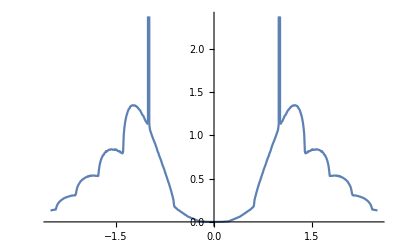

```mathematica
ListPlot[%33,Joined->True]
```

```mathematica
LaunchKernels[4]
```

```mathematica
c
```

```mathematica
Clear[left15]
```

```mathematica
left15[0]
```

{{0.,-0.582738,0.,0.248291,0.,-0.044418,0.,-0.0327466,0.,0.0288053,0.,-0.00170872,0.,-0.00951505,0.,0.00951505,0.,0.0112238,0.,-0.0270966,0.,0.00394126,0.,0.0771646,0.,-0.203873,0.,0.334447,0.,-0.417262},{-0.582738,0.,-0.334447,0.,0.203873,0.,-0.0771646,0.,-0.00394126,0.,0.0270966,0.,-0.0112238,0.,-0.00951505,0.,0.0302539,0.,-0.0141641,0.,-0.0519606,0.,0.113852,0.,-0.0822907,0.,-0.117717,0.,0.499924,0.},{0.,-0.334447,0.,-0.378865,0.,0.171127,0.,-0.0483593,0.,-0.00564998,0.,0.0175815,0.,-0.0112238,0.,0.0112238,0.,-0.00635776,0.,-0.0119315,0.,0.0540092,0.,-0.122767,0.,0.207738,0.,-0.286688,0.,0.334447},{0.248291,0.,-0.378865,0.,-0.411612,0.,0.199932,0.,-0.050068,0.,-0.015165,0.,0.0175815,0.,-0.00170872,0.,-0.0141641,0.,-0.0217067,0.,0.0996883,0.,-0.134251,0.,-0.00386507,0.,0.417633,0.,-0.117717,0.},{0.,0.203873,0.,-0.411612,0.,-0.382806,0.,0.198223,0.,-0.059583,0.,-0.015165,0.,0.0270966,0.,-0.0270966,0.,-0.0119315,0.,0.0747481,0.,-0.13864,0.,0.184583,0.,-0.205582,0.,0.207738,0.,-0.203873},{-0.044418,0.,0.171127,0.,-0.382806,0.,-0.384515,0.,0.188708,0.,-0.059583,0.,-0.00564998,0.,0.0288053,0.,-0.0519606,0.,0.0996883,0.,-0.103997,0.,-0.0180292,0.,0.365672,0.,-0.00386507,0.,-0.0822907,0.},{0.,-0.0771646,0.,0.199932,0.,-0.384515,0.,-0.39403,0.,0.188708,0.,-0.050068,0.,-0.00394126,0.,0.00394126,0.,0.0540092,0.,-0.13864,0.,0.205322,0.,-0.221455,0.,0.184583,0.,-0.122767,0.,0.0771646},{-0.0327466,0.,-0.0483593,0.,0.198223,0.,-0.39403,0.,-0.39403,0.,0.198223,0.,-0.0483593,0.,-0.0327466,0.,0.113852,0.,-0.134251,0.,-0.0180292,0.,0.395926,0.,-0.0180292,0.,-0.134251,0.,0.113852,0.},{0.,-0.00394126,0.,-0.050068,0.,0.188708,0.,-0.39403,0.,-0.384515,0.,0.199932,0.,-0.0771646,0.,0.0771646,0.,-0.122767,0.,0.184583,0.,-0.221455,0.,0.205322,0.,-0.13864,0.,0.0540092,0.,0.00394126},{0.0288053,0.,-0.00564998,0.,-0.059583,0.,0.188708,0.,-0.384515,0.,-0.382806,0.,0.171127,0.,-0.044418,0.,-0.0822907,0.,-0.00386507,0.,0.365672,0.,-0.0180292,0.,-0.103997,0.,0.0996883,0.,-0.0519606,0.},{0.,0.0270966,0.,-0.015165,0.,-0.059583,0.,0.198223,0.,-0.382806,0.,-0.411612,0.,0.203873,0.,-0.203873,0.,0.207738,0.,-0.205582,0.,0.184583,0.,-0.13864,0.,0.0747481,0.,-0.0119315,0.,-0.0270966},{-0.00170872,0.,0.0175815,0.,-0.015165,0.,-0.050068,0.,0.199932,0.,-0.411612,0.,-0.378865,0.,0.248291,0.,-0.117717,0.,0.417633,0.,-0.00386507,0.,-0.134251,0.,0.0996883,0.,-0.0217067,0.,-0.0141641,0.},{0.,-0.0112238,0.,0.0175815,0.,-0.00564998,0.,-0.0483593,0.,0.171127,0.,-0.378865,0.,-0.334447,0.,0.334447,0.,-0.286688,0.,0.207738,0.,-0.122767,0.,0.0540092,0.,-0.0119315,0.,-0.00635776,0.,0.0112238},{-0.00951505,0.,-0.0112238,0.,0.0270966,0.,-0.00394126,0.,-0.0771646,0.,0.203873,0.,-0.334447,0.,-0.582738,0.,0.499924,0.,-0.117717,0.,-0.0822907,0.,0.113852,0.,-0.0519606,0.,-0.0141641,0.,0.0302539,0.},{0.,-0.00951505,0.,-0.00170872,0.,0.0288053,0.,-0.0327466,0.,-0.044418,0.,0.248291,0.,-0.582738,0.,-0.417262,0.,0.334447,0.,-0.203873,0.,0.0771646,0.,0.00394126,0.,-0.0270966,0.,0.0112238,0.,0.00951505},{0.00951505,0.,0.0112238,0.,-0.0270966,0.,0.00394126,0.,0.0771646,0.,-0.203873,0.,0.334447,0.,-0.417262,0.,-0.499924,0.,0.117717,0.,0.0822907,0.,-0.113852,0.,0.0519606,0.,0.0141641,0.,-0.0302539,0.},{0.,0.0302539,0.,-0.0141641,0.,-0.0519606,0.,0.113852,0.,-0.0822907,0.,-0.117717,0.,0.499924,0.,-0.499924,0.,-0.382206,0.,0.200008,0.,-0.0315617,0.,-0.0618918,0.,0.0661247,0.,-0.0160898,0.,-0.0302539},{0.0112238,0.,-0.00635776,0.,-0.0119315,0.,0.0540092,0.,-0.122767,0.,0.207738,0.,-0.286688,0.,0.334447,0.,-0.382206,0.,-0.299916,0.,0.0861558,0.,0.020399,0.,-0.0477277,0.,0.0358708,0.,-0.0160898,0.},{0.,-0.0141641,0.,-0.0217067,0.,0.0996883,0.,-0.134251,0.,-0.00386507,0.,0.417633,0.,-0.117717,0.,0.117717,0.,-0.299916,0.,-0.413768,0.,0.138116,0.,0.034563,0.,-0.0779816,0.,0.0358708,0.,0.0141641},{-0.0270966,0.,-0.0119315,0.,0.0747481,0.,-0.13864,0.,0.184583,0.,-0.205582,0.,0.207738,0.,-0.203873,0.,0.200008,0.,-0.413768,0.,-0.361807,0.,0.152281,0.,0.00430916,0.,-0.0779816,0.,0.0661247,0.},{0.,-0.0519606,0.,0.0996883,0.,-0.103997,0.,-0.0180292,0.,0.365672,0.,-0.00386507,0.,-0.0822907,0.,0.0822907,0.,0.0861558,0.,-0.361807,0.,-0.347643,0.,0.122027,0.,0.00430916,0.,-0.0477277,0.,0.0519606},{0.00394126,0.,0.0540092,0.,-0.13864,0.,0.205322,0.,-0.221455,0.,0.184583,0.,-0.122767,0.,0.0771646,0.,-0.0315617,0.,0.138116,0.,-0.347643,0.,-0.377897,0.,0.122027,0.,0.034563,0.,-0.0618918,0.},{0.,0.113852,0.,-0.134251,0.,-0.0180292,0.,0.395926,0.,-0.0180292,0.,-0.134251,0.,0.113852,0.,-0.113852,0.,0.020399,0.,0.152281,0.,-0.377897,0.,-0.377897,0.,0.152281,0.,0.020399,0.,-0.113852},{0.0771646,0.,-0.122767,0.,0.184583,0.,-0.221455,0.,0.205322,0.,-0.13864,0.,0.0540092,0.,0.00394126,0.,-0.0618918,0.,0.034563,0.,0.122027,0.,-0.377897,0.,-0.347643,0.,0.138116,0.,-0.0315617,0.},{0.,-0.0822907,0.,-0.00386507,0.,0.365672,0.,-0.0180292,0.,-0.103997,0.,0.0996883,0.,-0.0519606,0.,0.0519606,0.,-0.0477277,0.,0.00430916,0.,0.122027,0.,-0.347643,0.,-0.361807,0.,0.0861558,0.,0.0822907},{-0.203873,0.,0.207738,0.,-0.205582,0.,0.184583,0.,-0.13864,0.,0.0747481,0.,-0.0119315,0.,-0.0270966,0.,0.0661247,0.,-0.0779816,0.,0.00430916,0.,0.152281,0.,-0.361807,0.,-0.413768,0.,0.200008,0.},{0.,-0.117717,0.,0.417633,0.,-0.00386507,0.,-0.134251,0.,0.0996883,0.,-0.0217067,0.,-0.0141641,0.,0.0141641,0.,0.0358708,0.,-0.0779816,0.,0.034563,0.,0.138116,0.,-0.413768,0.,-0.299916,0.,0.117717},{0.334447,0.,-0.286688,0.,0.207738,0.,-0.122767,0.,0.0540092,0.,-0.0119315,0.,-0.00635776,0.,0.0112238,0.,-0.0160898,0.,0.0358708,0.,-0.0477277,0.,0.020399,0.,0.0861558,0.,-0.299916,0.,-0.382206,0.},{0.,0.499924,0.,-0.117717,0.,-0.0822907,0.,0.113852,0.,-0.0519606,0.,-0.0141641,0.,0.0302539,0.,-0.0302539,0.,-0.0160898,0.,0.0661247,0.,-0.0618918,0.,-0.0315617,0.,0.200008,0.,-0.382206,0.,-0.499924},{-0.417262,0.,0.334447,0.,-0.203873,0.,0.0771646,0.,0.00394126,0.,-0.0270966,0.,0.0112238,0.,0.00951505,0.,-0.0302539,0.,0.0141641,0.,0.0519606,0.,-0.113852,0.,0.0822907,0.,0.117717,0.,-0.499924,0.}}

```mathematica
tr[0,0.0001,0.5,0,11]
```

1.

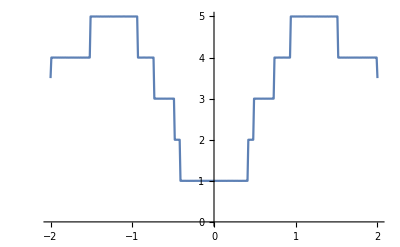
{5131.95,-Graphics-}

```mathematica
Timing[ListLinePlot[Table[{ω,Abs[tr[ω,0.0001,1,0,11]]},{ω,Range[-2,2,0.01]}]]]
```

```mathematica
Do[Export["/home/shardulmukim/PhD/fwi/AGNR/11AGNR/leads/sl"<>ToString[x]<>".dat",LEFT[x,0.0001,1,0,11]],{x,-2,2,0.01}]
```

```mathematica
tr1=Compile[{ω},tr[ω,0.0001,1,0,15],CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
left:=left= Compile[{ω,m},LEFT[ω,0.0001,1,0,m],CompilationTarget->"C"]
```

```mathematica
left[1,11]//MatrixForm
```

IdentityMatrix::dims: Dimension specification 22. should be a positive machine integer or a pair of positive machine integers.

ReplacePart::pkspec1: The expression 22. cannot be used as a part specification.

ReplacePart::pkspec1: The expression 20. cannot be used as a part specification.

ReplacePart::pkspec1: The expression 18. cannot be used as a part specification.

General::stop: Further output of ReplacePart::pkspec1 will be suppressed during this calculation.

IdentityMatrix::dims: Dimension specification -1 should be a positive machine integer or a pair of positive machine integers.

IdentityMatrix::dims: Dimension specification 22. should be a positive machine integer or a pair of positive machine integers.

General::stop: Further output of IdentityMatrix::dims will be suppressed during this calculation.

```mathematica
ListLinePlot[Table[{ω,-Im[LEFT[ω,0.0001,1,0,15][[1,1]]]},{ω,Range[-2,2,0.01]}]]//Timing
```

$Aborted

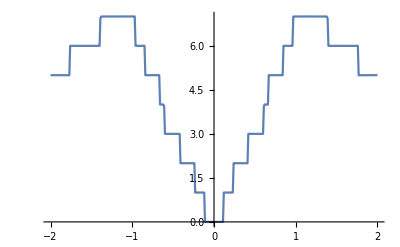
{21.4047,-Graphics-}

```mathematica
ListLinePlot[ParallelTable[{ω,tr1[ω]},{ω,Range[-2,2,0.01]}]]//Timing
```

```mathematica
m[ω_,δ_,t_,ϵ_,m_,ϵ1_]:=Module[{Tin=T1[t,m],T=ρ[t,m],μ1=RandomInteger[{1,2m}], μ2=RandomInteger[{1,2m}], μ3=RandomInteger[{1,2m}], μ4=RandomInteger[{1,2m}],μ5=RandomInteger[{1,2m}], μ6=RandomInteger[{1,2m}], μ7=RandomInteger[{1,2m}],μ8=RandomInteger[{1,2m}], μ9=RandomInteger[{1,2m}], μ10=RandomInteger[{1,2m}], μ11=RandomInteger[{1,2m}],μ12=RandomInteger[{1,2m}], μ13=RandomInteger[{1,2m}], μ14=RandomInteger[{1,2m}](*, μ15=RandomInteger[{8,42}],μ16=RandomInteger[{8,42}]*),J=LEFT[ω,δ,t,ϵ,m]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,t,0,m]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp4,imp11,imp4,imp,imp,imp3,imp13,imp11,imp,imp,imp,imp,imp,imp,imp,imp4,imp,imp,imp4,imp8,imp1,imp2,imp,imp10,imp,imp14,imp4,imp,imp10,imp10,imp,imp,imp1,imp,imp,imp3,imp9,imp,imp,imp2,imp,imp,imp12,imp,imp11,imp,imp,imp5,imp,imp7,imp8,imp,imp2,imp4,imp6,imp,imp,imp9,imp,imp,imp,imp,imp,imp7,imp,imp,imp,imp6,imp7,imp,imp,imp5,imp,imp,imp8,imp13,imp,imp,imp,imp9,imp,imp6,imp,imp,imp12,imp,imp14,imp,imp14,imp,imp13,imp3,imp,imp,imp,imp,imp1,imp5,imp,imp,imp,imp12,imp}]};
sl1= Module[{},Do[J=Inverse[IdentityMatrix[2m]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];
 J=J];
Il1:=Inverse[IdentityMatrix[2m]-sl1.T.J.T].sl1;
Ir1:=Inverse[IdentityMatrix[2m]-J.T.sl1.T].J;gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= J.T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,δ,t,ϵ,m],tr[ω,δ,t,ϵ,m],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
ca=Compile[{ω},m[ω,0.0001,1,0,11,0.5],CompilationTarget->"C"(*,CompilationOptions->{"ExpressionOptimization" -> True}*)]
```

CompiledFunction[…]

```mathematica
Mean[ParallelTable[ca[1],2000]]//AbsoluteTiming
```

{32.6428,2.84586}

```mathematica
Mean[ParallelTable[ca[1],2000]]//AbsoluteTiming
```

{36.2604,2.85704}

```mathematica
Table[Mean[ParallelTable[ca[ω],2000]],{ω,-2,2,0.5}]
```

{2.07577,1.72479,2.829,1.03507,0.706202,1.08881,2.84564,1.49565,0.868283}